```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v3/datav3

```mathematica
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,870,960,5}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,870,960,5}];
r422=chi4/chi2;
(*r422[[1]]=r422[[1]][[17;;-1]];*)
Export["r42data_tosmooth.dat",r422]
```

r42data_tosmooth.dat

```mathematica
Dimensions[r422]
```

{19,104}

```mathematica
mub=Table[i,{i,870,960,5}];
T=Table[i,{i,17,120,1}];
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r422[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
Export["r42high.dat",R42all]
```

r42high.dat

```mathematica
Length[chi2[[2]]]
```

104

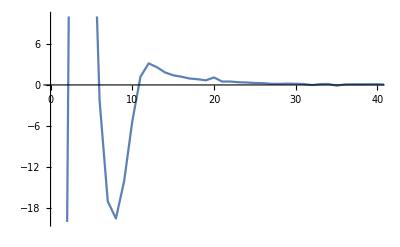

```mathematica
ListLinePlot[r422[[6]],PlotRange->{{0,40},{-20,10}}]
```

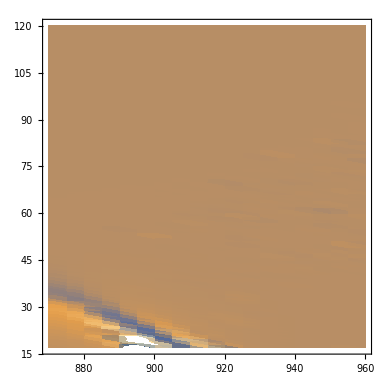

```mathematica
ListDensityPlot[R42all,PlotRange->{All,All,{-25,40}}]
```

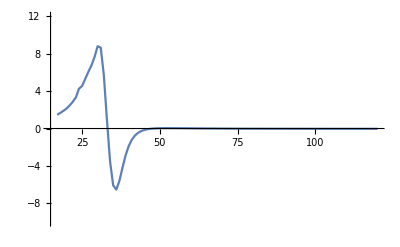

```mathematica
ListLinePlot[{Transpose[{T,r422[[1]]}]},PlotRange->{All,{-10,12}}]
```

```mathematica
smoothr42=Import["./output.dat"];
```

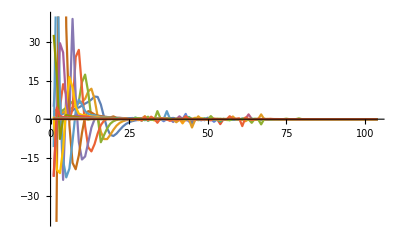

```mathematica
ListLinePlot[smoothr42[[1;;19]],PlotRange->{All,{-40,40}}]
```